```mathematica
Needs["utilities`"]
Needs["MaTeX`"];
Get[FileNameJoin@{NotebookDirectory[],"generalizedKlyshkoCriteria.m"}]

Qprobs[λs_,s_]:=poisson[λs,s]s!
```

```mathematica
optimizeSample[listOfPoints_List]:=listOfPoints//Do[Which[
idx==1,Sow@#⟦idx⟧,
#⟦idx,2⟧≠#⟦idx-1,2⟧,Sow@#⟦idx⟧,
idx==Length@#,Sow@#⟦idx⟧,
#⟦idx,2⟧≠#⟦idx+1,2⟧,Sow@#⟦idx⟧
],{idx,Length@#}]&//Reap//Last//Last;
ClearAll@makeRectReprBoundaries;
makeRectReprBoundaries[data_List,colorRules_:{True->Red,False->Blue}]:=With[{pairs=Partition[data,2]},
Table[
{pair⟦1,2⟧/.colorRules,Rectangle[{pair⟦1,1⟧,0},{pair⟦2,1⟧,1}]},
{pair,pairs}
]
];
```

```mathematica
fig=With[{vSpacing=0.6,p=0.5},
Module[{probsVsμ},
probsVsμ[μ_]=photonAddedCohMixedWithCoh[μ,p,{0,1,2,3,4,5}];
With[{regionBoundaries=(optimizeSample@Table[
{μ,klyshkoBasicCriteria[#,probsVsμ[μ]]>0},
{μ,0.001,6,0.0001}
])&/@{1,2}},
Graphics[{
(* create K1 rectangles *)
Scale[#,{1,0.5}]&@makeRectReprBoundaries@regionBoundaries⟦1⟧,
Scale[#,{1,0.5}]&@Translate[makeRectReprBoundaries@regionBoundaries⟦2⟧,{0,vSpacing}],
(* create Kinf rectangles *)
(Scale[#,{1,0.5}]&@Translate[
makeRectReprBoundaries[
optimizeSample@Table[
{μ,Quiet@klyshkoInfCriterion[#,probsVsμ[μ]]>0},
{μ,0.001,6,0.001}
],
{True->Darker@Red,False->Darker@Blue}
],
{0,(#)vSpacing}])&/@{2,3},
Inset[MaTeX["\\mathcal K_1",Magnification->1.5],{6.5,0.5}],
Inset[MaTeX["\\mathcal K_2",Magnification->1.5],{6.5,0.5+vSpacing}],
Inset[MaTeX["\\mathcal K_{\\infty,2}",Magnification->1.5],{6.5,0.5+2vSpacing}],
Inset[MaTeX["\\mathcal K_{\\infty,3}",Magnification->1.5],{6.5,0.5+3vSpacing}],
(* create horizontal axis *)
With[{vShift=0},
{Thick,Arrow@{{0,vShift},{7,vShift}},
Inset[MaTeX["\\mu",Magnification->1.5],{7.3,vShift}],
Table[
{Line@{{s,vShift-0.05},{s,vShift+0.05}},
Inset[MaTeX[s,Magnification->1.3],{s,vShift-0.36}]},
{s,0,6,1}
]
}]
}]
]]]
```

-Graphics-

```mathematica
squeezedVacuumProbs[n_List,r_]:=squeezedVacuumProbs[#,r]&/@n;
squeezedVacuumProbs[n_,r_]:=If[OddQ@n,0,
(n!)/(2^n((n/2)!)^2)Tanh[r]^n/(Cosh@r)
];
```

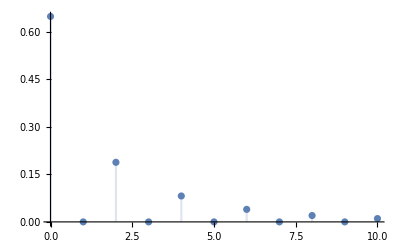

```mathematica
DiscretePlot[squeezedVacuumProbs[n,1],{n,0,10},PlotRange->All]
```

```mathematica
Sum[N@squeezedVacuumProbs[n,1.3],{n,0,3000}]
```

1.

```mathematica
squeezedVacuumProbs[{1,2,3},r]
```

{0,1/2 Sech[r] Tanh[r]^2,0}

```mathematica
fig=With[{vSpacing=0.6,r=0.5},
Module[{probsVsμ},
probsVsμ[μ_]=squeezedVacuumProbs[{0,1,2,3,4,5},r];
With[{regionBoundaries=(optimizeSample@Table[
{μ,klyshkoBasicCriteria[#,probsVsμ[μ]]>0},
{μ,0.001,6,0.0001}
])&/@{1,2}},
Graphics[{
(* create K1 rectangles *)
Scale[#,{1,0.5}]&@makeRectReprBoundaries@regionBoundaries⟦1⟧,
Scale[#,{1,0.5}]&@Translate[makeRectReprBoundaries@regionBoundaries⟦2⟧,{0,vSpacing}],
(* create Kinf rectangles *)
(Scale[#,{1,0.5}]&@Translate[
makeRectReprBoundaries[
optimizeSample@Table[
{μ,Quiet@klyshkoInfCriterion[#,probsVsμ[μ]]>0},
{μ,0.001,6,0.001}
],
{True->Darker@Red,False->Darker@Blue}
],
{0,(#)vSpacing}])&/@{2,3},
Inset[MaTeX["\\mathcal K_1",Magnification->1.5],{6.5,0.5}],
Inset[MaTeX["\\mathcal K_2",Magnification->1.5],{6.5,0.5+vSpacing}],
Inset[MaTeX["\\mathcal K_{\\infty,2}",Magnification->1.5],{6.5,0.5+2vSpacing}],
Inset[MaTeX["\\mathcal K_{\\infty,3}",Magnification->1.5],{6.5,0.5+3vSpacing}],
(* create horizontal axis *)
With[{vShift=0},
{Thick,Arrow@{{0,vShift},{7,vShift}},
Inset[MaTeX["\\mu",Magnification->1.5],{7.3,vShift}],
Table[
{Line@{{s,vShift-0.05},{s,vShift+0.05}},
Inset[MaTeX[s,Magnification->1.3],{s,vShift-0.36}]},
{s,0,6,1}
]
}]
}]
]]]
```

-Graphics-

```mathematica
klyshkoInfCriterion[2]//extractParameters
```

{P[0],P[1],P[2]}

```mathematica
klyshkoInfCriterion[2]
```

-1+P[0]+((-1+ⅇ^((2 P[2])/P[1])) P[1]^2)/(2 P[2])

```mathematica
klyshkoInfCriterion[2,squeezedVacuumProbs[{0,1,2,3},r]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Indeterminate

## Thermal squeezed states

```mathematica
ClearAll[p0,p1,p2]
p0[mn_,V_]:=2 √(V/((1+2 mn+V) (1+V+2 mn V)));
p1[mn_,V_]:=(8 mn (1+mn))/(((1+2 mn+V) (1+V+2 mn V))/V)^(3/2);
p2[mn_,V_]:=(√V (1+4 mn (1+mn)-2 V^2+8 mn (1+mn) (-1+4 mn (1+mn)) V^2+(1+2 mn)^2 V^4))/((1+2 mn+V) (1+V+2 mn V))^(5/2);
squeezedThermalProbs[mn_,V_]:=#[mn,V]&/@{p0,p1,p2};
```

```mathematica
klyshkoBasicCriteria[1]
```

P[1]^2-2 P[0] P[2]

```mathematica
With[{mn=0.4,v=0.2},klyshkoBasicCriteria[1,squeezedThermalProbs[mn,v]]]
```

-0.126684

```mathematica
squeezedThermalProbs[μ,v]
```

{2 √(v/((1+v+2 μ) (1+v+2 v μ))),(8 μ (1+μ))/(((1+v+2 μ) (1+v+2 v μ))/v)^(3/2),(√v (1-2 v^2+4 μ (1+μ)+v^4 (1+2 μ)^2+8 v^2 μ (1+μ) (-1+4 μ (1+μ))))/((1+v+2 μ) (1+v+2 v μ))^(5/2)}

```mathematica
klyshkoBasicCriteria[1]
```

P[1]^2-2 P[0] P[2]

```mathematica
Plot3D[
klyshkoBasicCriteria[1,squeezedThermalProbs[μ,v]],
{μ,0,4},{v,0,1},
PlotRangePadding->None,ColorFunction->"TemperatureMap",
LabelStyle->Directive[Thick,FontFamily->"Latin Modern Math",FontSize->22,Black],
ImageSize->500
]
```

-Graphics3D-

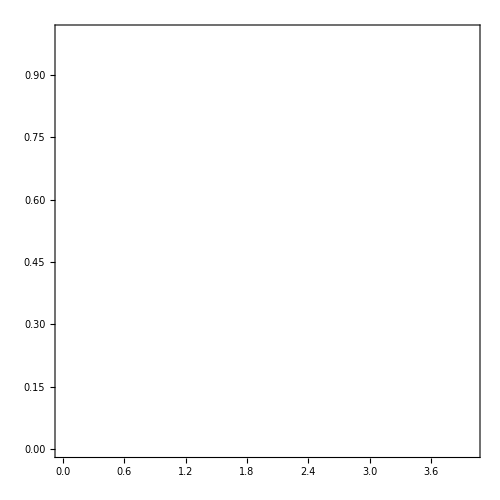

```mathematica
RegionPlot[
{
klyshkoBasicCriteria[1,squeezedThermalProbs[μ,v]]>0
},
{μ,0,4},{v,0,1},
PlotRangePadding->None,
LabelStyle->Directive[Thick,FontFamily->"Latin Modern Math",FontSize->22,Black],
FrameLabel->{MaTeX["\\mu",Magnification->2.4],MaTeX["e^{-2\\xi}",Magnification->2.4]},FrameStyle->Thick,
ImageSize->500
]~Show~Plot[1/0.43 1/Sqrt@mu,{mu,0,4},PlotStyle->Red]
```

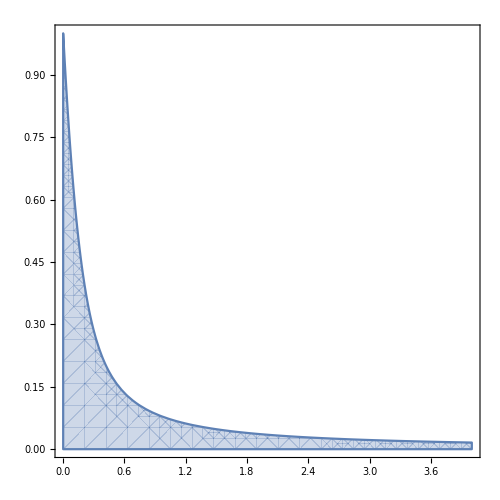

```mathematica
fig=RegionPlot[
{
Re@klyshkoInfCriterion[2,squeezedThermalProbs[μ,v]]>0,
klyshkoBasicCriteria[1,squeezedThermalProbs[μ,v]]>0},
{μ,0,4},{v,0,1},
PlotRangePadding->None,
LabelStyle->Directive[Thick,FontFamily->"Latin Modern Math",FontSize->22,Black],
FrameLabel->{MaTeX["\\mu",Magnification->2.4],MaTeX["e^{-2\\xi}",Magnification->2.4]},FrameStyle->Thick,
ImageSize->500
](*~Show~ContourPlot[x y==.08,{x,0,4},{y,0,1},ContourStyle->Red]*)
```

```mathematica
Export[FileNameJoin@{"/home/lk/Documents/docs/research/Radim/draft/figures/","squeezedThermalStateNonclassicalityP012.pdf"},
fig]
```

/home/lk/Documents/docs/research/Radim/draft/figures/squeezedThermalStateNonclassicalityP012.pdf

```mathematica
SystemOpen@"/home/lk/Documents/docs/research/Radim/draft/figures"
```